```mathematica
Sum[Sum[SphericalHarmonicY[l,m,θp,ϕp]SphericalHarmonicY[l,m,θ,ϕ],{m,-l,l}],{l,0,Infinity}]
```

∑_(l=0)^∞ (∑_(m=-l)^l SphericalHarmonicY[l,m,θ,ϕ] SphericalHarmonicY[l,m,θp,ϕp])

```mathematica
Assuming[0<a&&0<b&&Element[{l,m},Integers]&&Element[{r,ω},Reals],DSolve[(a^2-b^2 r^2)(1/r^2 D[r^2 D[u[r],r],r]-1/r^2(l(l+1))u[r]-ω^2 u[r])==λ u[r],u[r],r]]
```

{{u[r]→DifferentialRoot[Function[{y,x},{(-a^2 l+x^2 b^2 l-a^2 l^2+x^2 b^2 l^2-x^2 λ-x^2 a^2 ω^2+x^4 b^2 ω^2) y[x]+2 x (a-x b) (a+x b) y'[x]+x^2 (a-x b) (a+x b) y''[x]==0,y[1]==C[1],y'[1]==C[2]}]][r]}}

```mathematica
Assuming[0<a&&0<b&&Element[{l,m},Integers]&&a/b>r>0&&Element[{ω},Reals],FullSimplify[DSolve[S'[r]^2==(λ+ω)/(a^2-b^2 r^2)+(l(l+1))/r^2,S[r],r]]]
```

{{S[r]→1/(2 b)(2 b C[1]+b √l √(1+l) (-2 Log[r]+Log[2 l (a-b r) (a+b r)+2 l^2 (a-b r) (a+b r)+r^2 (λ+ω)+2 √l √((1+l) (a-b r) (a+b r)) √(a^2 l (1+l)+r^2 (-b^2 l (1+l)+λ+ω))])+√(b^2 l (1+l)-λ-ω) Log[a^2 (-2 b^2 l (1+l)+λ+ω)+2 b (b^3 l (1+l) r^2-b r^2 (λ+ω)+√((a-b r) (a+b r) (b^2 l (1+l)-λ-ω)) √(a^2 l (1+l)+r^2 (-b^2 l (1+l)+λ+ω)))])},{S[r]→1/(2 b)(2 b C[1]+b √l √(1+l) (2 Log[r]-Log[2 l (a-b r) (a+b r)+2 l^2 (a-b r) (a+b r)+r^2 (λ+ω)+2 √l √((1+l) (a-b r) (a+b r)) √(a^2 l (1+l)+r^2 (-b^2 l (1+l)+λ+ω))])-√(b^2 l (1+l)-λ-ω) Log[a^2 (-2 b^2 l (1+l)+λ+ω)+2 b (b^3 l (1+l) r^2-b r^2 (λ+ω)+√((a-b r) (a+b r) (b^2 l (1+l)-λ-ω)) √(a^2 l (1+l)+r^2 (-b^2 l (1+l)+λ+ω)))])}}

```mathematica
{{S[r]->1/(2 b)(2 b C[1]+b √(l(1+l)) (-2 Log[r]+Log[2l(l+1)(v[r]^2 +r^2 (λ+ω)/(l (1+l))+v[r]  √(v[r]^2+r^2 (λ+ω)/(l (1+l))))])+√(b^2 l (1+l)-λ-ω) Log[-2 a^2 l (1+l)( b^2 -1/2(λ+ω)/(l (1+l)))+2 b l (1+l) (b r^2(b^2-(λ+ω)/(l (1+l)))+v[r] √(b^2-(λ+ω)/(l (1+l))) √(v[r]^2+r^2(λ+ω)/(l (1+l))))])},{S[r]->1/(2 b)(2 b C[1]+b √l √(1+l) (2 Log[r]-Log[2 l (a-b r) (a+b r)+2 l^2 (a-b r) (a+b r)+r^2 (λ+ω)+2 √l √((1+l) (a-b r) (a+b r)) √(a^2 l (1+l)+r^2 (-b^2 l (1+l)+λ+ω))])-√(b^2 l (1+l)-λ-ω) Log[a^2 (-2 b^2 l (1+l)+λ+ω)+2 b (b^3 l (1+l) r^2-b r^2 (λ+ω)+√((a-b r) (a+b r) (b^2 l (1+l)-λ-ω)) √(a^2 l (1+l)+r^2 (-b^2 l (1+l)+λ+ω)))])}}
```

```mathematica
1/r Sqrt[(((λ+ω)-l(l+1))b^2 r^2+l(l+1)a^2)/(a^2-b^2 r^2)]
```

(√((a^2 l (1+l)+b^2 r^2 (-l (1+l)+λ+ω))/(a^2-b^2 r^2)))/r

```mathematica
Assuming[Element[{α,β,γ,δ},Reals],FullSimplify[Integrate[1/x Sqrt[(α x^2+β)/(γ x^2+δ)],x]]]
```

-((x^2 α+β) √((x^2 α+β)/(x^2 γ+δ)) √((α (x^2 γ+δ))/(-β γ+α δ)) AppellF1[3/2,1/2,1,5/2,((x^2 α+β) γ)/(β γ-α δ),1+(x^2 α)/β])/(3 β)

```mathematica
Q[r_]:=(λ+ω)/(a^2-b^2 r^2)+(l(l+1))/r^2;
```

```mathematica
S0p[r_]:=Sqrt[Q[r]];
```

```mathematica
Assuming[0<a&&0<b&&Element[{l,m},Integers]&&a/b>r>0&&Element[{ω},Reals],FullSimplify[D[S0p[r],r]+2S0p[r]S1'[r]+2/r S0p[r]==0]]
```

```mathematica
Assuming[0<a&&0<b&&Element[{l,m},Integers]&&a/b>r>0&&Element[{ω},Reals],DSolve[1/(√((l (1+l))/r^2+(λ+ω)/(a^2-b^2 r^2)))(a^4 l (1+l)+b^2 r^4 (b^2 l (1+l)-λ-ω)+2 a^2 r^2 (-b^2 l (1+l)+λ+ω)+2 r (a-b r) (a+b r) (a^2 l (1+l)+r^2 (-b^2 l (1+l)+λ+ω)) S1'[r])==0,S1[r],r]]
```

{{S1[r]→C[1]+1/2 (-Log[r]+1/2 Log[a^2-b^2 r^2]-1/2 Log[a^2 l+a^2 l^2-b^2 l r^2-b^2 l^2 r^2+r^2 λ+r^2 ω])}}

```mathematica
S1[r]->C[1]+1/2 (-Log[r]+1/2 Log[v[r]^2]-1/2 Log[v[r]^2 l(1+l)+r^2(λ+ ω)])
```

```mathematica
S1[r_]:=Const1-1/4 Log[r^2 l(1+l)+r^4/v[r]^2(λ+ ω)]
```

```mathematica
S0[r_]:=Const0+(√((1+l)l))/2 (-2 Log[r]+Log[2 l (a-b r) (a+b r)+2 l^2 (a-b r) (a+b r)+r^2 (λ+ω)+2 √l √((1+l) (a-b r) (a+b r)) √(a^2 l (1+l)+r^2 (-b^2 l (1+l)+λ+ω))])+1/(2b)√(b^2 l (1+l)-λ-ω) Log[a^2 (-2 b^2 l (1+l)+λ+ω)+2 b (b^3 l (1+l) r^2-b r^2 (λ+ω)+√((a-b r) (a+b r) (b^2 l (1+l)-λ-ω)) √(a^2 l (1+l)+r^2 (-b^2 l (1+l)+λ+ω)))]
```

```mathematica
S0[r_]:=Const0+(√((1+l)l))/2 (Log[λ+ω+2 l (1+l) v[r]/r^2 (v[r]+√((r^2 (λ+ω))/(l (1+l))+v[r]^2))]+√(1 -1/b^2(λ+ω)/(l (1+l))) Log[2 b^2 (-(a^2 (λ+ω))/(2 b^2)-(-1+(λ+ω)/(b^2 (l+l^2))) v[r]^2+l (1+l) √(1-(λ+ω)/(b^2 l (1+l))) v[r] √((r^2 (λ+ω))/(l (1+l))+v[r]^2))])
```

```mathematica
Assuming[0<a&&0<b&&Element[{l,m},Integers]&&a/b>r>0&&Element[{ω},Reals],FullSimplify[Const0+(√((1+l)l))/2 (Log[λ+ω+2 l (1+l) v[r]/r^2 (v[r]+√((r^2 (λ+ω))/(l (1+l))+v[r]^2))]+√(1 -1/b^2(λ+ω)/(l (1+l))) Log[2 b^2 (-(a^2 (λ+ω))/(2 b^2)-(-1+(λ+ω)/(b^2 (l+l^2))) v[r]^2+l (1+l) √(1-(λ+ω)/(b^2 l (1+l))) v[r] √((r^2 (λ+ω))/(l (1+l))+v[r]^2))])]]
```

Const0+1/2 √(l (1+l)) (√(1-(λ+ω)/(b^2 l (1+l))) Log[2 b^2 (-(a^2 (λ+ω))/(2 b^2)-(-1+(λ+ω)/(b^2 (l+l^2))) v[r]^2+l (1+l) √(1-(λ+ω)/(b^2 l (1+l))) v[r] √((r^2 (λ+ω))/(l (1+l))+v[r]^2))]+Log[λ+ω+(2 l (1+l) v[r] (v[r]+√((r^2 (λ+ω))/(l (1+l))+v[r]^2)))/r^2])

```mathematica
Assuming[0<a&&0<b&&Element[{l,m},Integers]&&a/b>r>0&&Element[{ω},Reals],DSolve[r^2 S'[r]^2==-(r^2(λ-ω^2)+l(l+1))/(a^2-b^2 r^2),S[r],r]]
```

{{S[r]→((a^2-b^2 r^2) √((l+l^2+r^2 (λ-ω^2))/(-a^2+b^2 r^2)) AppellF1[1/2,-1/2,1,3/2,((a^2-b^2 r^2) (λ-ω^2))/(b^2 l (1+l)+a^2 (λ-ω^2)),1-(b^2 r^2)/a^2])/(a^2 √((b^2 (l+l^2+r^2 (λ-ω^2)))/(b^2 l (1+l)+a^2 (λ-ω^2))))+C[1]},{S[r]→(r (-a^2+b^2 r^2) √((l+l^2+r^2 (λ-ω^2))/(-a^2 r^2+b^2 r^4)) AppellF1[1/2,-1/2,1,3/2,((a^2-b^2 r^2) (λ-ω^2))/(b^2 l (1+l)+a^2 (λ-ω^2)),1-(b^2 r^2)/a^2])/(a^2 √((b^2 (l+l^2+r^2 (λ-ω^2)))/(b^2 l (1+l)+a^2 (λ-ω^2))))+C[1]}}

```mathematica
Assuming[0<a&&0<b&&Element[{l,m},Integers]&&a/b>r>0&&Element[{ω},Reals],FullSimplify[{{S[r]->((a^2-b^2 r^2) √((l+l^2+r^2 (λ-ω^2))/(-a^2+b^2 r^2)) AppellF1[1/2,-1/2,1,3/2,((a^2-b^2 r^2) (λ-ω^2))/(b^2 l (1+l)+a^2 (λ-ω^2)),1-(b^2 r^2)/a^2])/(a^2 √((b^2 (l+l^2+r^2 (λ-ω^2)))/(b^2 l (1+l)+a^2 (λ-ω^2))))+C[1]},{S[r]->((-a^2+b^2 r^2) √((l+l^2+r^2 (λ-ω^2))/(-a^2 +b^2 r^2)) AppellF1[1/2,-1/2,1,3/2,((a^2-b^2 r^2) (λ-ω^2))/(b^2 l (1+l)+a^2 (λ-ω^2)),1-(b^2 r^2)/a^2])/(a^2 √((b^2 (l+l^2+r^2 (λ-ω^2)))/(b^2 l (1+l)+a^2 (λ-ω^2))))+C[1]}}]]
```

```mathematica
FullSimplify[{{S[r]->(I √v[r] AppellF1[1/2,-1/2,1,3/2,((a-b r) (a+b r) (λ-ω^2))/(b^2 l (1+l)+a^2 (λ-ω^2)),1-(b^2 r^2)/a^2])/(a^2 b √(1/(b^2 l (1+l)+a^2 (λ-ω^2))))+C[1]},{S[r]->-(I √v[r] AppellF1[1/2,-1/2,1,3/2,((a-b r) (a+b r) (λ-ω^2))/(b^2 l (1+l)+a^2 (λ-ω^2)),1-(b^2 r^2)/a^2])/(a^2 b √(1/(b^2 l (1+l)+a^2 (λ-ω^2))))+C[1]}}]
```

```mathematica
Assuming[0<a&&0<b&&Element[{l,m},Integers]&&a/b>r>0&&Element[{ω},Reals],FullSimplify[{{S[r]->C[1]+(1/(a^2 b)ⅈ AppellF1[1/2,-1/2,1,3/2,((a-b r) (a+b r) (λ-ω^2))/(b^2 l (1+l)+a^2 (λ-ω^2)),1-(b^2 r^2)/a^2] √((b^2 l (1+l)+a^2 (λ-ω^2))v[r]))},{S[r]->C[1]-1/(a^2 b)ⅈ AppellF1[1/2,-1/2,1,3/2,((a-b r) (a+b r) (λ-ω^2))/(b^2 l (1+l)+a^2 (λ-ω^2)),1-(b^2 r^2)/a^2] √((b^2 l (1+l)+a^2 (λ-ω^2))v[r])}}]]
```

```mathematica
Assuming[0<a&&0<b&&Element[{l,m},Integers]&&a/b>r>0&&Element[{ω},Reals],FullSimplify[{{S[r]->C[1]+1/(a^2 b)ⅈ AppellF1[1/2,-1/2,1,3/2,(v[r] (λ-ω^2))/(b^2 l (1+l)+a^2 (λ-ω^2)),v[r]/a^2] √((b^2 l (1+l)+a^2 (λ-ω^2)) v[r])},{S[r]->C[1]-1/(a^2 b)ⅈ AppellF1[1/2,-1/2,1,3/2,(v[r] (λ-ω^2))/(b^2 l (1+l)+a^2 (λ-ω^2)),v[r]/a^2] √((b^2 l (1+l)+a^2 (λ-ω^2)) v[r])}}]]
```

{{S[r]→C[1]+(ⅈ AppellF1[1/2,-1/2,1,3/2,((λ-ω^2) v[r])/(b^2 l (1+l)+a^2 (λ-ω^2)),v[r]/a^2] √((b^2 l (1+l)+a^2 (λ-ω^2)) v[r]))/(a^2 b)},{S[r]→C[1]-(ⅈ AppellF1[1/2,-1/2,1,3/2,((λ-ω^2) v[r])/(b^2 l (1+l)+a^2 (λ-ω^2)),v[r]/a^2] √((b^2 l (1+l)+a^2 (λ-ω^2)) v[r]))/(a^2 b)}}

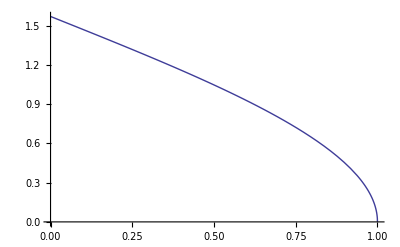

```mathematica
Plot[Sqrt[1-r^2]AppellF1[1/2,-1/2,1,3/2,1-r^2,1-r^2] ,{r,0,1}]
```

```mathematica
-(r^2(λ-ω^2)+l(l+1))/(r^2(a^2-b^2 r^2))
```